# Tic tac toe

Ref: http://www.divertimentosinformaticos.com/2011/06/la-maquina-invencible.html

## Minimax strategy

The minimax strategy consists on creating a tree of all the possible outcomes of the game. In each step it selects the best branch according to which have the best probable outcome.

```mathematica
CreateBoard[]:=ConstantArray[" ",{3,3}];
WinnerQ[board_,player_]:=Module[{horizontals,verticals,diagonalRight,diagonalLeft,all,results},
horizontals = Table[board[[i]],{i,1,3}];
verticals = Table[board[[All,i]],{i,1,3}];
diagonalRight =Table[board[[i,i]],{i,1,3}];
diagonalLeft = Table[board[[i,-i]],{i,1,3}];
all = Join[horizontals,verticals,{diagonalLeft},{diagonalRight}];
results = Map[Apply[SameQ,Append[#,player]]&,all];
Return[Apply[Or,results]];
];

AnotherPlayer[player_]:=Switch[player,"x","o","o","x"];
ReturnValueTarget[player_,target_]:=If[player==target,1,-1];
PrintBoard[board_]:=Grid[board,Frame->All];
PossibleMovements[board_,currentplayer_,minMaxState_,targetPlayer_]:=Module[{m,availablePositions,strategies},
If[Length[Position[board, "x"|"o"]]==0,
Return[

{
{board->({{currentplayer, " ", " "}, {" ", " ", " "}, {" ", " ", " "}}),0},
{board->({{" ", " ", " "}, {currentplayer, " ", " "}, {" ", " ", " "}}),0},
{board->({{" ", " ", " "}, {" ", currentplayer, " "}, {" ", " ", " "}}),0}
}
];
];

(* Check if there is a draw *)
availablePositions = Position[board," "];
If[Length[availablePositions] == 0, Return[{}]];

(* Get results of every possible next strategy *)
strategies = Table[
{pos,Last[MinMaxStrategy[ReplacePart[board,pos->currentplayer],AnotherPlayer[currentplayer],!minMaxState,targetPlayer]]},
{pos,availablePositions}
];
Return[Map[{board->ReplacePart[board,First[#]->currentplayer],Last[#]}&,strategies]];
];


MinMaxStrategy[board_,currentplayer_,minMaxState_,targetPlayer_]:=Module[{availablePositions,strategies,bestMove},
If[Length[Position[board, "x"|"o"]]==0,
Return[{RandomInteger[{1,3},2]}];
];

(* Check if a player has won *)
If[WinnerQ[board,"x"], Return[{Null,ReturnValueTarget["x",targetPlayer]}]];
If[WinnerQ[board,"o"], Return[{Null,ReturnValueTarget["o",targetPlayer]}]];

(* Check if there is a draw *)
availablePositions = Position[board," "];
If[Length[availablePositions] == 0, Return[{Null,0}]];

(* Get results of every possible next strategy *)
strategies = Table[
{pos,Last[MinMaxStrategy[ReplacePart[board,pos->currentplayer],AnotherPlayer[currentplayer],!minMaxState,targetPlayer]]},
{pos,availablePositions}
];

If[Length[strategies] == 1,Return[First[strategies]]];

If[minMaxState,
bestMove = First[MaximalBy[strategies,Last]];
,
bestMove =First[MinimalBy[strategies,Last]];
];
Return[bestMove];
];
```

## Explore every strategy

```mathematica
Concatenate[l_/;Length[l]>1]:=Apply[Join,l];
Concatenate[l_/;Length[l]==1]:=First[l];

Iterate[states_List,currentplayer_,minMaxState_,targetPlayer_]:=
{
Concatenate[
Map[
PossibleMovements[#,currentplayer,minMaxState,targetPlayer]&,
states
]
]
,
AnotherPlayer[currentplayer]
,
!minMaxState
};
GoDeeper[states_,currentplayer_,minMaxState_,targetPlayer_]:=Iterate[states[[All,1,2]],currentplayer,minMaxState,targetPlayer];

Explore[]:=Block[{states,player,minMax,explored},
{states,player,minMax} = Iterate[{CreateBoard[]},"o",True,"x"];
explored = {states};

While[states ≠ {},
{states,player,minMax} = GoDeeper[states,player,minMax,"o"];
AppendTo[explored,states];
];

Return[DeleteDuplicates[Concatenate[explored]]];
];

Explore[n_]:=Block[{states,player,minMax,explored},
{states,player,minMax} = Iterate[{CreateBoard[]},"o",True,"x"];
explored = {states};

Do[
{states,player,minMax} = GoDeeper[states,player,minMax,"o"];
AppendTo[explored,states];
,
n
];

Return[DeleteDuplicates[Concatenate[explored]]];
];
```

```mathematica
exploration = Explore[];
```

```mathematica
graph = Map[{PrintBoard[First[First[#]]]->PrintBoard[Last[First[#]]],Last[#]}&,Take[exploration,100]];
```

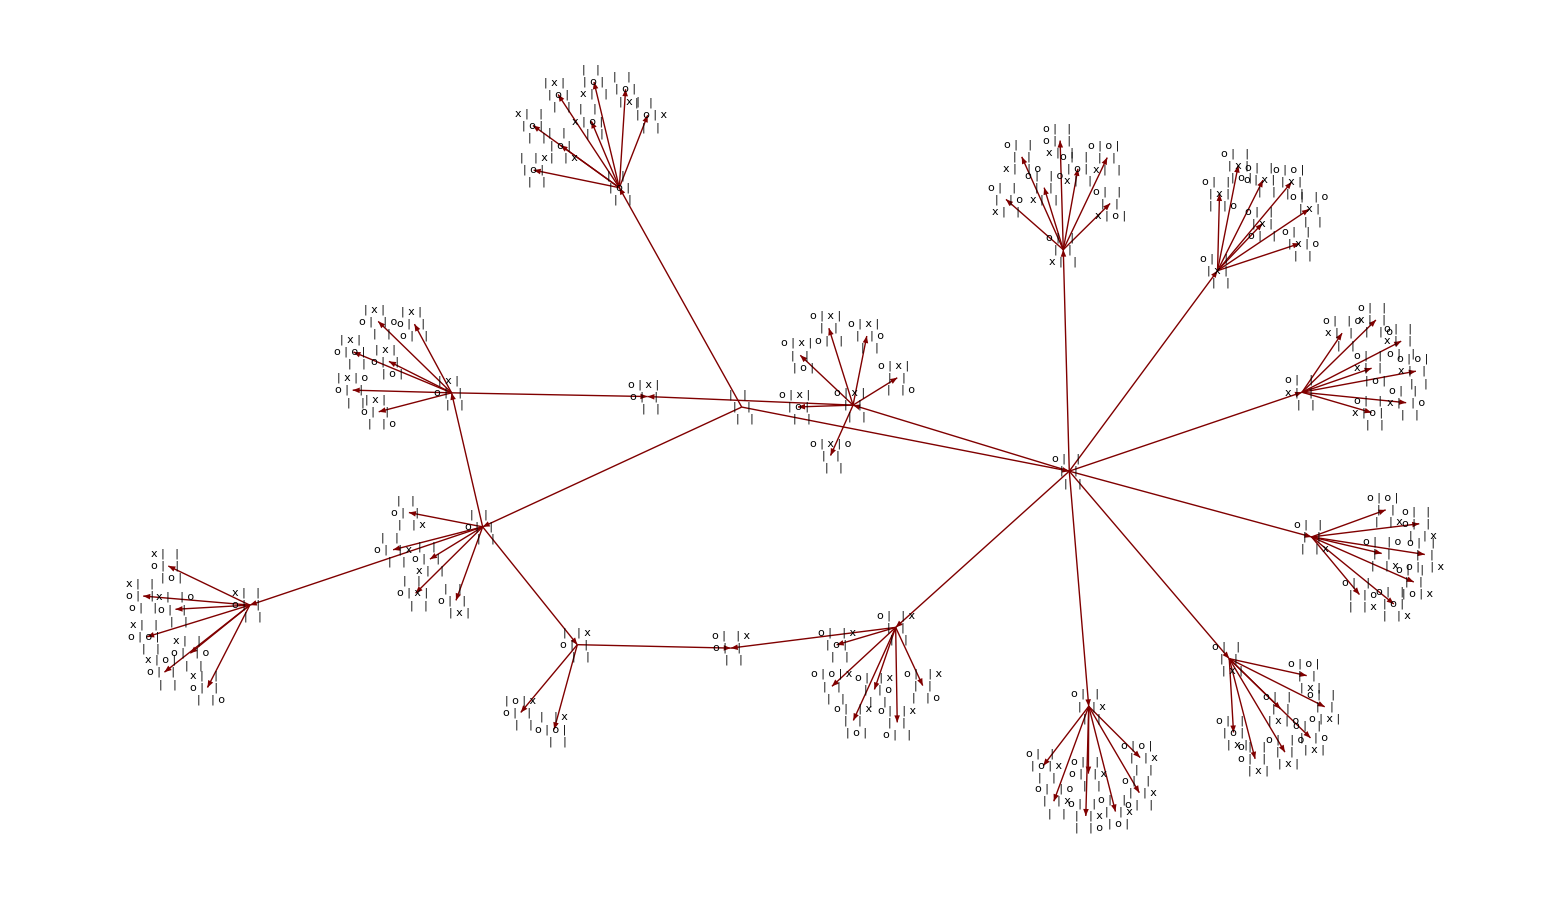

```mathematica
GraphPlot[graph,VertexLabeling->True]
```

```mathematica
graph = Map[{PrintBoard[First[First[#]]]->PrintBoard[Last[First[#]]],Last[#]}&,Take[exploration,1000]];
```

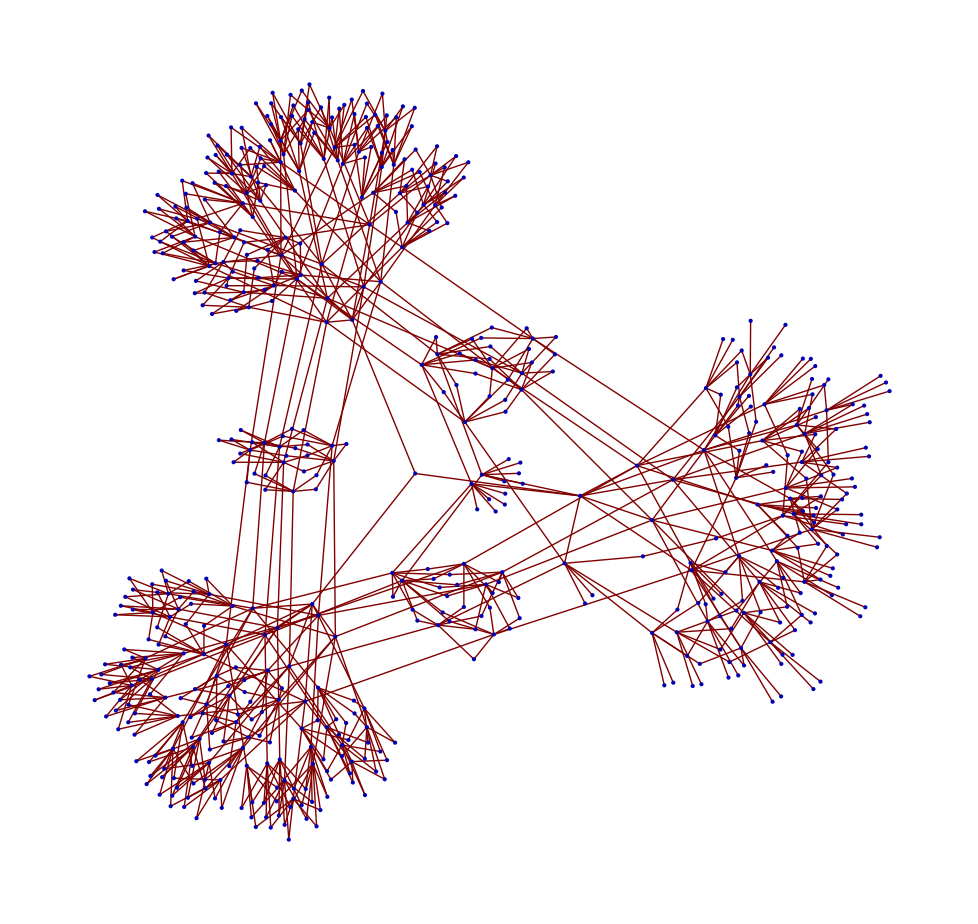

```mathematica
GraphPlot[graph,EdgeLabeling->False]
```

## GUI

```mathematica
board = CreateBoard[];
styling = {"x"->Style["x", FontSize->100,FontColor->Red],"o"->Style["o", FontSize->100,FontColor->Blue], " "->Style[" ", FontSize->100]};
DynamicModule[{enemyMove,interactiveElements, playing = True},
Dynamic[
interactiveElements = MapIndexed[
Button[#1 /.styling,
If[#1 == " " && playing,

(* Process player movement *)
board = ReplacePart[board,#2->"o"];
If[WinnerQ[board,"o"], 
playing = False;
Print["The player has won!"];
];

(* Process machine movement *)
enemyMove = First[MinMaxStrategy[board,"x",False,"o"]];
If[Length[enemyMove]>0,
board = ReplacePart[board,enemyMove->"x"];
If[WinnerQ[board,"x"], 
playing = False;
Print["The machine has won..."];
];
,
Print["Game over"];
];
],Method->"Queued"
]&,board,
{2}
];
Grid[interactiveElements ,Frame->All],
TrackedSymbols:>{board}
]
]
```

Game over